```mathematica
Quit[]
```

total number of errors and warnings
===================================
fferr: no errors

```mathematica
$LoadFeynArts=True;
<<FeynCalc`
```

FeynCalc 9.2.0. For help, use the documentation center, check out the wiki or write to the mailing list.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput. Phys. Commun., 207C, 432-444, 2016, arXiv:1601.01167

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun., 64, 345-359, 1991.

FeynArts 3.11 (2 Sep 2019) patched for use with FeynCalc, for documentation use the manual or visit www.feynarts.de.

```mathematica
$FAVerbose=0;
```

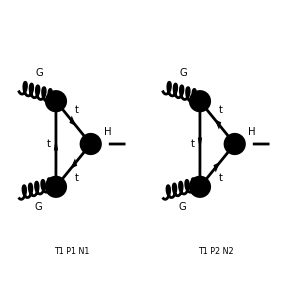

FeynArtsGraphics({G,G}→{H})(([T1 P1 N1] | [T1 P2 N2] | Null
Null | Null | Null
Null | Null | Null))

```mathematica
diags=InsertFields[CreateTopologies[1,2->1,ExcludeTopologies->{SelfEnergies}],{V[4],V[4]}->{S[1]},InsertionLevel->{Particles},Model->"htt",GenericModel->"htt",LastSelections->{F[9]}];
Paint[diags]
```

```mathematica
amp=FCFAConvert[CreateFeynAmp[diags,Truncated->True],IncomingMomenta->{p[1],p[2]},OutgoingMomenta->{p[3]},LoopMomenta->{l},DropSumOver->True,ChangeDimension->4,UndoChiralSplittings->True]/.M$FACouplings/.{FCGV["MT"]->MT,FAGS->gs,ybcky->yt};
```

```mathematica
amp
```

{(tr((γ̄·(l̄+OverBar[p(2)]-OverBar[p(3)])+MT).((yt (γ̄)^6 (sin(al)-ⅈ cos(al)))/(√2)+(yt (γ̄)^7 (-sin(al)-cos(al)) (sin(al)+ⅈ cos(al)))/(√2 (sin(al)+cos(al)))).(γ̄·(l̄+OverBar[p(2)])+MT).(-ⅈ gs (γ̄)^Lor2 T_Col4Col5^Glu2).(γ̄·l̄+MT).(-ⅈ gs (γ̄)^Lor1 T_Col5Col4^Glu1)))/(16 π^4 ((l̄)^2-MT^2).((l̄+OverBar[p(2)])^2-MT^2).((l̄+OverBar[p(2)]-OverBar[p(3)])^2-MT^2)),(tr((γ̄·(l̄+OverBar[p(2)]-OverBar[p(3)])+MT).((yt (γ̄)^6 (sin(al)-ⅈ cos(al)))/(√2)+(yt (γ̄)^7 (-sin(al)-cos(al)) (sin(al)+ⅈ cos(al)))/(√2 (sin(al)+cos(al)))).(γ̄·(l̄+OverBar[p(2)])+MT).(ⅈ gs (γ̄)^Lor2 T_Col5Col4^Glu2).(γ̄·l̄+MT).(ⅈ gs (γ̄)^Lor1 T_Col4Col5^Glu1)))/(16 π^4 ((l̄)^2-MT^2).((l̄+OverBar[p(2)])^2-MT^2).((l̄+OverBar[p(2)]-OverBar[p(3)])^2-MT^2))}

```mathematica
Plus@@amp/.{DiracTrace->TR}//Contract//SUNSimplify//FullSimplify//ChangeDimension[#,D]&
```

(ⅈ gs^2 MT yt δ^Glu1Glu2 (cos(al) (g^Lor1Lor2 (-l^2+MT^2-p(2)·p(3)+q)+2 l^Lor1 (2 l^Lor2+(p(2))^Lor2)-(p(3))^Lor1 (2 l^Lor2+(p(2))^Lor2)+(p(2))^Lor1 (2 l^Lor2+(p(3))^Lor2))+sin(al) ϵ^(Lor1Lor2p(2)p(3))))/(4 √2 π^4 (l^2-MT^2).((l+p(2))^2-MT^2).((l+p(2)-p(3))^2-MT^2))

```mathematica
ampt=Plus@@amp//Contract//TR//SUNSimplify//FullSimplify//ChangeDimension[#,D]&;
```

```mathematica
ampt
```

(ⅈ gs^2 MT yt δ^Glu1Glu2 (cos(al) (g^Lor1Lor2 (-l^2+MT^2+(p(2))^2-p(2)·p(3))+2 l^Lor1 (2 l^Lor2+(p(2))^Lor2)-(p(3))^Lor1 (2 l^Lor2+(p(2))^Lor2)+(p(2))^Lor1 (2 l^Lor2+(p(3))^Lor2))+sin(al) ϵ^(Lor1Lor2p(2)p(3))))/(√2 π^4 (l^2-MT^2).((l+p(2))^2-MT^2).((l+p(2)-p(3))^2-MT^2))

```mathematica
ampt=ampt/.{p[3]->p[1]+p[2]}
```

(ⅈ gs^2 MT yt δ^Glu1Glu2 (cos(al) (g^Lor1Lor2 (-p(2)·(p(1)+p(2))-l^2+MT^2+(p(2))^2)+2 l^Lor1 (2 l^Lor2+(p(2))^Lor2)-(p(1)+p(2))^Lor1 (2 l^Lor2+(p(2))^Lor2)+(p(2))^Lor1 (2 l^Lor2+(p(1)+p(2))^Lor2))+sin(al) ϵ^(Lor1Lor2p(2)p(1)+p(2))))/(√2 π^4 (l^2-MT^2).((l+p(2))^2-MT^2).((l+p(2)-(p(1)+p(2)))^2-MT^2))

```mathematica
FCClearScalarProducts[];
SPD[p[1],p[1]]=0;
SPD[p[2],p[2]]=q;
SPD[p[1],p[2]]=(MH^2-q)/2;
```

```mathematica
ampt=TID[ampt,l,ToPaVe->True]//Simplify;
```

```mathematica
ampt
```

1/(2 √2 π^2 (D-2) (MH^2-q)^3)gs^2 MT yt δ^Glu1Glu2 ((MH^2-q) (4 (D-2) cos(al) (p(1))^Lor1 B_0(0,MT^2,MT^2) ((p(2))^Lor2 (q-MH^2)+2 q (p(1))^Lor2)+C_0(MH^2,0,q,MT^2,MT^2,MT^2) (cos(al) (MH^2-q)^2 g^Lor1Lor2 ((D-2) MH^2-(D-2) q-8 MT^2)-2 (MH^2-q) (cos(al) (p(2))^Lor1 (p(1))^Lor2 ((D-2) MH^2-(D-2) q-8 MT^2)-(D-2) sin(al) (MH^2-q) ϵ^(Lor1Lor2p(1)p(2)))+2 cos(al) (p(1))^Lor1 ((D-2) MH^2+(D-2) q+8 MT^2) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)))+4 cos(al) B_0(q,MT^2,MT^2) (-(p(1))^Lor1 ((D-2) MH^2+D q) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)+q (MH^2-q)^2 g^Lor1Lor2+2 q (p(2))^Lor1 (p(1))^Lor2 (q-MH^2))+2 cos(al) B_0(MH^2,MT^2,MT^2) ((MH^2-q)^2 ((D-4) MH^2-(D-2) q) g^Lor1Lor2-2 (p(2))^Lor1 (p(1))^Lor2 (MH^2-q) ((D-4) MH^2-(D-2) q)+2 (p(1))^Lor1 (D (MH^2+q)-2 q) ((p(2))^Lor2 (MH^2-q)-2 q (p(1))^Lor2)))

```mathematica
Cases[ampt,_B0,Infinity]//DeleteDuplicates//StandardForm
```

{B0[q,MT^2,MT^2],B0[MH^2,MT^2,MT^2],B0[0,MT^2,MT^2]}

```mathematica
Cases[ampt,_C0,Infinity]//DeleteDuplicates//StandardForm
```

{C0[Pair[Momentum[p[1],D],Momentum[p[1],D]],Pair[Momentum[p[2],D],Momentum[p[2],D]],Pair[Momentum[p[1],D],Momentum[p[1],D]]+2 Pair[Momentum[p[1],D],Momentum[p[2],D]]+Pair[Momentum[p[2],D],Momentum[p[2],D]],MT^2,MT^2,MT^2]}

```mathematica
beta=Sqrt[4 MT^2/MH^2-1];
beta1=Sqrt[1-4 MT^2/q];
scalarIntegral={_C0->(1/2/(q-MH^2) (Log[(beta1+1)/(beta1-1)]^2+ ArcTan[2 beta/(1-beta^2)]^2)),
B0[MH^2,MT^2,MT^2]->(1/ep+Log[m^2/MH^2]+2-beta ArcTan[2 beta/(beta^2-1)]-Log[(1+beta^2)/4]),
B0[q,MT^2,MT^2]->(1/ep+Log[m^2/(-q)]+2+beta1 Log[beta1-1]-beta1 Log[beta1+1]-Log[(beta1^2-1)/4]),
B0[0,MT^2,MT^2]->(1/ep+Log[m^2/MT^2])};
```

```mathematica
tmp=Series[ampt/.scalarIntegral//ChangeDimension[#,4]&//ReplaceAll[#,{D->4-2 ep}]&,{ep,0,0}]//Normal//Simplify
```

1/(4 √2 π^2 (MH^2-q)^3)gs^2 MT yt δ^Glu1Glu2 (4 cos(al) (log(-m^2/q)+√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-√(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-log(-MT^2/q)+2) (q (MH^2-q)^2 (ḡ)^Lor1Lor2+2 q (q-MH^2) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2-2 (MH^2+2 q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))+2 cos(al) (log(m^2/MH^2)-log(MT^2/MH^2)+√((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))+2) (-2 q (MH^2-q)^2 (ḡ)^Lor1Lor2+4 q (MH^2-q) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2+4 (2 MH^2+q) OverBar[p(1)]^Lor1 ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-1/2 ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))) (2 cos(al) (MH^2-q)^2 (MH^2-4 MT^2-q) (ḡ)^Lor1Lor2-2 (MH^2-q) (2 cos(al) OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2 (MH^2-4 MT^2-q)+2 sin(al) (q-MH^2) ϵ^(Lor1Lor2 OverBar[p(1)]OverBar[p(2)]))+4 cos(al) OverBar[p(1)]^Lor1 (MH^2+4 MT^2+q) ((MH^2-q) OverBar[p(2)]^Lor2-2 q OverBar[p(1)]^Lor2))-4 cos(al) (MH^2-q)^3 (ḡ)^Lor1Lor2-4 cos(al) (MH^2-q) OverBar[p(1)]^Lor1 (2-2 log(m^2/MT^2)) ((q-MH^2) OverBar[p(2)]^Lor2+2 q OverBar[p(1)]^Lor2)+8 cos(al) (MH^2-q)^2 OverBar[p(2)]^Lor1 OverBar[p(1)]^Lor2)

```mathematica
Cases[tmp,_Pair,Infinity]//DeleteDuplicates//StandardForm
```

{Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],Pair[LorentzIndex[Lor1],Momentum[p[2]]],Pair[LorentzIndex[Lor2],Momentum[p[1]]],Pair[LorentzIndex[Lor1],Momentum[p[1]]],Pair[LorentzIndex[Lor2],Momentum[p[2]]]}

```mathematica
structure=Coefficient[tmp,{Pair[LorentzIndex[Lor1],LorentzIndex[Lor2]],Pair[LorentzIndex[Lor1],Momentum[p[2]]] Pair[LorentzIndex[Lor2],Momentum[p[1]]],Pair[LorentzIndex[Lor1],Momentum[p[2]]] Pair[LorentzIndex[Lor2],Momentum[p[2]]]}]//Simplify;
```

```mathematica
structure[[1]]/SPD[p[1],p[2]]
```

1/(2 √2 π^2 (MH^2-q)^2)gs^2 MT yt cos(al) δ^Glu1Glu2 (-4 q log(m^2/MH^2)+4 q log(-m^2/q)+MH^2 (-log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1)))+4 q log(MT^2/MH^2)+(-MH^2+4 MT^2+q) (tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2-4 q √((4 MT^2)/MH^2-1) tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2))-4 MH^2+4 MT^2 log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))+q log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))+4 q √(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)-1)-4 q √(1-(4 MT^2)/q) log(√(1-(4 MT^2)/q)+1)-4 q log(-MT^2/q)+4 q)

```mathematica
tmp1=structure[[2]]//FullSimplify[#,MT>0 && MH>0 && q<0 && m>0 && MT>MH]&;
```

```mathematica
tmp1
```

(gs^2 MT yt cos(al) δ^Glu1Glu2 ((MH^2-4 MT^2-q) log^2(1-(q (√(1-(4 MT^2)/q)+1))/(2 MT^2))+(MH^2-4 MT^2-q) (tan^-1((MH √(4 MT^2-MH^2))/(MH^2-2 MT^2)))^2+4 q √((4 MT^2)/MH^2-1) tan^-1((MH √(4 MT^2-MH^2))/(MH^2-2 MT^2))+4 (MH^2-q)+8 q √(1-(4 MT^2)/q) coth^-1(√(1-(4 MT^2)/q))))/(2 √2 π^2 (MH^2-q)^2)

```mathematica
tmp2=Series[tmp1,{q,-Infinity,1}]//Normal//FullSimplify[#,q<0 && MT>0 && MH>0 && MT>MH]&
```

-(gs^2 MT yt cos(al) δ^Glu1Glu2 (MH ((tan^-1((MH √(4 MT^2-MH^2))/(MH^2-2 MT^2)))^2+(log(-MT^2/q)+2)^2)-4 √(4 MT^2-MH^2) tan^-1((MH √(4 MT^2-MH^2))/(MH^2-2 MT^2))))/(2 √2 π^2 MH q)

```mathematica
Series[tmp2,{MT,Infinity,1}]
```

(gs^2 yt cos(al) δ^Glu1Glu2)/(3 √2 π^2 MT)+O((1/MT)^2)

```mathematica
Cases[tmp,_Eps,Infinity]//DeleteDuplicates//StandardForm
```

{Eps[LorentzIndex[Lor1],LorentzIndex[Lor2],Momentum[p[1]],Momentum[p[2]]]}

```mathematica
Coefficient[tmp,Eps[LorentzIndex[Lor1],LorentzIndex[Lor2],Momentum[p[1]],Momentum[p[2]]]]//Simplify
```

-(gs^2 MT yt sin(al) δ^Glu1Glu2 ((tan^-1((MH^2 √((4 MT^2)/MH^2-1))/(MH^2-2 MT^2)))^2+log^2((√(1-(4 MT^2)/q)+1)/(√(1-(4 MT^2)/q)-1))))/(2 √2 π^2 (MH^2-q))

```mathematica
Install["LoopTools"]
```

====================================================
   FF 2.0, a package to evaluate one-loop integrals
 written by G. J. van Oldenborgh, NIKHEF-H, Amsterdam
 ====================================================
 for the algorithms used see preprint NIKHEF-H 89/17,
 'New Algorithms for One-loop Integrals', by G.J. van
 Oldenborgh and J.A.M. Vermaseren, published in 
 Zeitschrift fuer Physik C46(1990)425.
 ====================================================

LinkObject[…]

```mathematica
C0[0,172^2,125^2,172^2,172^2,172^2]
```

-0.0000194652

```mathematica
B0[-172^2,0,0]
```

-8.29499